```mathematica
(* Import RHP library and set directory for files *)
AppendTo[$Path, " Your path to the RHPackage-master package here "];
<<RiemannHilbert`;
```

```mathematica
(* Set n - genus *)
n=2; 
ϕ={0.1,0.2,0.3};
```

```mathematica
nt=2^8 (* Number points in t domain *);
nλ=40;(* parameter p in GG *)
```

```mathematica
λ={-1+3I,5I,1+3I}
```

{-1+3 ⅈ,5 ⅈ,1+3 ⅈ}

```mathematica
(* Riemann surface *)
w[z_]:=Product[√((z-Conjugate[λ[[i]]])/(z-λ[[i]]))(z-λ[[i]]), {i,n+1}] (* Why calculating this way? *);
```

```mathematica
K[ k_, j_]:= N[NIntegrate[(I(Re[λ[[j]]]+I x)^(k-1))/w[(Re[λ[[j]]]+I x-10^-10)],{x, -Im[λ[[j]]], Im[λ[[j]]]}]] (* 10^-10 to avoid singylarity? *);
```

```mathematica
(* Here the solving of linear equation system for Cf with Cf0=0 *)
If [n>1,Cf=Join[{0},LinearSolve[Transpose[Table[K[k, j], {j, 2, n+1}, {k, 1, n}]], Join[ConstantArray[0, n-1], {-2Pi I}]]],Cf=Join[{0},LinearSolve[Transpose[Table[K[k, j], {j, 2, n+1}, {k, 1, n}]],  {-2Pi I}]]]
```

{0,8.43082+2.83636×10^-7 ⅈ,16.8616-1.88755×10^-12 ⅈ}

```mathematica
(* W0 is a free term of asymptotic series of w(z)/(ξ-z) z->∞ to calculate f0 *)
W0[ξ_]=SeriesCoefficient[Simplify[Series[w[z]/(ξ-z), {z, Infinity, 1}]], 0];
```

```mathematica
(* Calculation f0 *)
f00=1/(2π I)Total[Table[Cf[[j]] N[NIntegrate[(I W0[Re[λ[[j]]]+I x])/w[(Re[λ[[j]]]+I x-10^-10)],{x, -Im[λ[[j]]], Im[λ[[j]]]}]], {j,1, n+1}]]
```

4.21538-5.91265×10^-7 ⅈ

```mathematica
(* Correction λ for periodicity *)
λ=λ+0 Re[f00]
```

{-1.+3. ⅈ,0.+5. ⅈ,1.+3. ⅈ}

```mathematica
(* --------------------- Riemann surface for redefined λ and all again --------------------------------- *)
w[z_]:=Product[√((z-Conjugate[λ[[i]]])/(z-λ[[i]]))(z-λ[[i]]), {i,n+1}];
K[ k_, j_]:= N[NIntegrate[(I(Re[λ[[j]]]+I x)^(k-1))/w[(Re[λ[[j]]]+I x-10^-10)],{x, -Im[λ[[j]]], Im[λ[[j]]]}]];
If [n>1,Cf=Join[{0},LinearSolve[Transpose[Table[K[k, j], {j, 2, n+1}, {k, 1, n}]], Join[ConstantArray[0, n-1], {-2Pi I}]]],Cf=Join[{0},LinearSolve[Transpose[Table[K[k, j], {j, 2, n+1}, {k, 1, n}]],  {-2Pi I}]]]
```

{0,8.43082+2.83646×10^-7 ⅈ,16.8616-1.88969×10^-12 ⅈ}

```mathematica
(* Again W0 *)
W0[ξ_]=SeriesCoefficient[Simplify[Series[w[z]/(ξ-z), {z, Infinity, 1}]], 0];
```

```mathematica
(* Calculating f0 *)
f0=1/(2π I)Total[Table[Cf[[j]] N[NIntegrate[(I W0[Re[λ[[j]]]+I x])/w[(Re[λ[[j]]]+I x-10^-10)],{x, -Im[λ[[j]]], Im[λ[[j]]]}]], {j,1, n+1}]]
If[Abs[f0]>10^-3, Print["f_0 is too large"]]
```

4.21538+9.71316×10^-8 ⅈ

f_0 is too large

```mathematica
(* Siganl period for Subscript[C, 1]^f=-2ΔReλ *)
Tnorm=Abs[2π/Min[Re[Cf[[2;;]]]]]
```

0.745264

```mathematica
(* Jump matrix *)
Clear[G];
G[_][_,_?InfinityQ]:=IdentityMatrix[2];
G[_][_,_?ZeroQ]:=IdentityMatrix[2];
Do[G[i][x_,z_]=({{0z, I Exp[-I(Cf[[i]] x)]Exp[-I ϕ[[i]]]}, {I Exp[I(Cf[[i]]x)]Exp[I ϕ[[i]]], 0z}})/.Underflow[]->0, {i, 1, n+1}];
```

```mathematica
(* Preparation Fun with G and main spectrum for Solver *)
GG[p_,x_]:=Table[Fun[G[j][x,#]&,Line[{Re[λ[[j]]]-I Im[λ[[j]]],Re[λ[[j]]]+I Im[λ[[j]]]}],p],{j,1,n+1}];
(* Points in t domain *)
trange=Range[-Tnorm/2, Tnorm/2, Tnorm/(nt-1)]+Tnorm/2 ;
```

```mathematica
q1=0 trange;
For[ix=1,ix<=Length[trange],ix++,
U=RHSolve[GG[nλ,trange[[ix]]]];
q1[[ix]]=-1/π DomainIntegrate[U][[1,2]] ;
];
q2=0 trange;
For[ix=1,ix<=Length[trange],ix++,
q2[[ix]]=q1[[ix]]*Exp[2 ⅈ f0 trange[[ix]]];
];
```

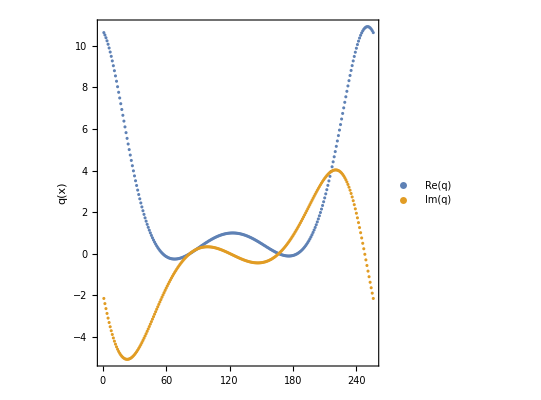

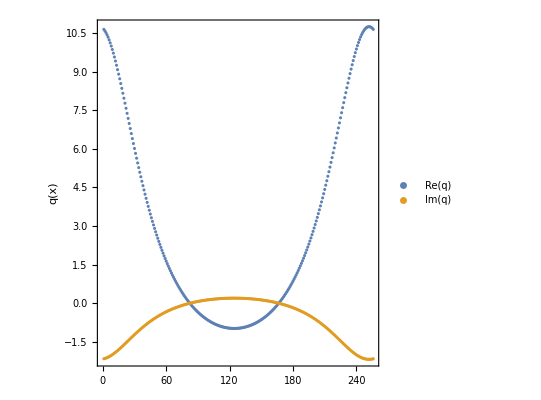

```mathematica
(* Signal plot *)
p1=ListPlot[{Re[q1], Im[q1]}, Frame->True, FrameStyle->Directive[Medium, Bold], PlotStyle->Bold,FrameLabel->{None,"q(x)"}, PlotLegends->Placed[{"Re(q)", "Im(q)"}, Above], AspectRatio->1,PlotRange->All]
p1=ListPlot[{Re[q2], Im[q2]}, Frame->True, FrameStyle->Directive[Medium, Bold], PlotStyle->Bold,FrameLabel->{None,"q(x)"}, PlotLegends->Placed[{"Re(q)", "Im(q)"}, Above], AspectRatio->1,PlotRange->All]
```

```mathematica
(* --------------- Retrieve phases back --------------------- *)
qfun=Interpolation[Partition[Riffle[trange, q2],2], InterpolationOrder->6];
```

```mathematica
(* Solving of Zakharov-Shabat problem M(λ)=Φ(Subscript[τ, 0],Subscript[τ, 0]+T,λ) *)
MM[k_]:=N[NDSolveValue[{D[Φ[t],t]==Dot[({{-I k, qfun[t]}, {-Conjugate[qfun[t]], I k}}),Φ[t]], Φ[0]==IdentityMatrix[2]}, Φ[Tnorm], {t, 0, Tnorm}]];
U=RHSolve[GG[1000,0]];
q00=q2[[1]];
Print["q(00)=", q2[[1]]]
```

q(00)=10.6428-2.1574 ⅈ

-6.69416+0.00120545 ⅈ

-6.69416+0.00120445 ⅈ

-6.69416+0.00120522 ⅈ

-6.69416+0.00120395 ⅈ

-6.69416+0.00120545 ⅈ

-6.69415+0.0012011 ⅈ

-2.10606+0.41612 ⅈ

-2.10606+0.416119 ⅈ

-2.10606+0.416119 ⅈ

-2.10606+0.416119 ⅈ

-2.10606+0.416126 ⅈ

-2.10606+0.416119 ⅈ

-2.10606+0.416119 ⅈ

-2.10606+0.416118 ⅈ

-2.10606+0.416119 ⅈ

-2.10606+0.416118 ⅈ

-2.10606+0.416119 ⅈ

-2.10606+0.416119 ⅈ

2.10613+0.416079 ⅈ

2.10613+0.416079 ⅈ

2.10613+0.416079 ⅈ

«3 more identical outputs»

2.10613+0.41608 ⅈ

2.10613+0.416079 ⅈ

2.10613+0.416079 ⅈ

2.10613+0.416079 ⅈ

2.10613+0.416077 ⅈ

2.10613+0.416079 ⅈ

6.69423+0.00120666 ⅈ

6.69423+0.00120665 ⅈ

6.69423+0.00120665 ⅈ

6.69423+0.00120665 ⅈ

6.69423+0.00120653 ⅈ

11.571+0.000402918 ⅈ

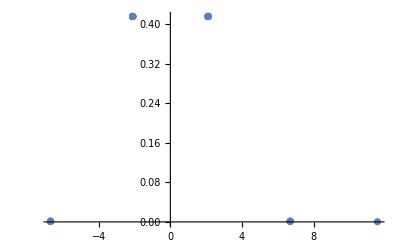

```mathematica
(* Procedure to calculate auxiliary spectrum *)
R2=Flatten[Table[{x+I y},{x,-5.1,5,2.0},{y,-5.1,5.0,2.0}]];
ϵ=10^-6;

For[rn=1,rn≤Length[R2],rn++,
r=R2[[rn]];
For[n1=1,n1<300,n1++,
r1=r-(MM[r][[1,2]])/(1/(2ϵ)((MM[r+ϵ][[1,2]]-MM[r][[1,2]])-I(MM[r+I ϵ][[1,2]]-MM[r][[1,2]])));
If[Abs[r1-r]<10^-5,Break,r=r1]];
R2[[rn]]=r;
Print[r];
]
ListPlot[Table[{Re[R2[[n]]],Im[R2[[n]]]},{n,1,Length[R2]}], PlotRange->All]
```

```mathematica
(* Auxiliary spectrum from procedure below *)
M[z_]:=(MM[z][[1,1]]+MM[z][[2,2]])^2-4;
M[-2.106061484518932+0.41611934941047884 ⅈ]
M[2.106128936036313+0.416078671308225 ⅈ]


mu1:=-2.106061484518932+0.41611934941047884 ⅈ;
mu2:=2.106128936036313+0.416078671308225 ⅈ;
Print["M_{12}(mu1)=", MM[mu1][[1,2]]]
Print["M_{12}(mu2)=", MM[mu2][[1,2]]]
```

-3.04924+0.354747 ⅈ

-3.04902-0.354735 ⅈ

M_{12}(mu1)=5.55054×10^-11-1.29586×10^-10 ⅈ

M_{12}(mu2)=-3.68898×10^-9-5.54523×10^-10 ⅈ

```mathematica
(* Introducing polynomials, directly*)
P[z1_]:=(z1-λ[[1]])(z1-λ[[2]])(z1-λ[[3]])(z1-Conjugate[λ[[1]]])(z1-Conjugate[λ[[2]]])(z1-Conjugate[λ[[3]]]);
g[z1_]:=q00(z1-mu1)(z1-mu2);
h[z1_]:=-Conjugate[q00](z1-Conjugate[mu1])(z1-Conjugate[mu2]);
CoefficientList[P[z1]+g[z1] h[z1],z1]
CoefficientList[(z^3+AA z^2+BB z + CC)^2,z]
aa:=(0+0.ⅈ)/2;
bb:= (-76.92341391836996+0.ⅈ-aa^2)/2;
cc:=(0.015908226407077564+0.ⅈ)/2-aa bb;
Print["Checking coeff"]
cc^2
2 bb cc
bb^2+2 aa cc
2 aa bb + 2 cc
aa^2+2 bb
2 aa
F[z_]:=z^3+aa z^2+bb z + cc;

(* Checking if mu_i is a pole *)
Print["Checking if mu_i is a pole, ie not zero of F-w"]
F[mu1]-w[mu1]
F[mu2]-w[mu2]

Print["Checking if conj mu_i is a pole"]
F[Conjugate[mu1]]-w[Conjugate[mu1]]
F[Conjugate[mu2]]-w[Conjugate[mu2]]

Print["Checking if  conj mu_i is a zero of F+w"]
F[Conjugate[mu1]]+w[Conjugate[mu1]]
F[Conjugate[mu2]]+w[Conjugate[mu2]]

Print["Checking if mu_i is a zero of F+w"]
F[mu1]+w[mu1]
F[mu2]+w[mu2]
```

{-4.78893+0. ⅈ,-0.0509939+0. ⅈ,1505.3+0. ⅈ,0.0159082+0. ⅈ,-76.9234+0. ⅈ,0,1}

{CC^2,2 BB CC,BB^2+2 AA CC,2 AA BB+2 CC,AA^2+2 BB,2 AA,1}

Checking coeff

0.0000632679+0. ⅈ

-0.611858+0. ⅈ

1479.3+0. ⅈ

0.0159082+0. ⅈ

-76.9234+0. ⅈ

0.+0. ⅈ

Checking if mu_i is a pole, ie not zero of F-w

146.272-21.2806 ⅈ

-146.26-21.2786 ⅈ

Checking if conj mu_i is a pole

146.272+21.2806 ⅈ

-146.26+21.2786 ⅈ

Checking if  conj mu_i is a zero of F+w

-0.745934-0.201359 ⅈ

0.762322-0.202173 ⅈ

Checking if mu_i is a zero of F+w

-0.745934+0.201359 ⅈ

0.762322+0.202173 ⅈ

R(infty)=0.00021213-0.000320027 ⅈ

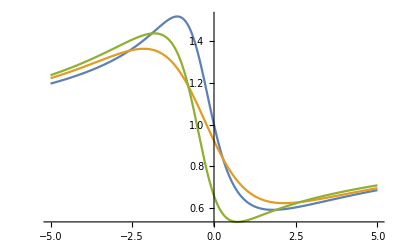

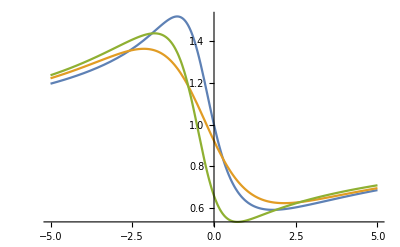

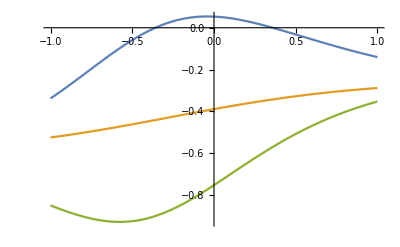

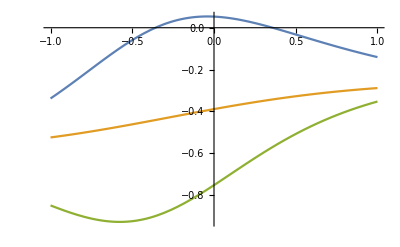

```mathematica
(* Introducing J00^2 *)
R[z2_]:=-I/h[z2](F[z2]-w[z2]);
Print["R(infty)=", R[10000-10000I] ] (* Checking branch, should be 0 *)
 
J002[z4_]:=-(ⅇ^(4z4 ⅈ Tnorm))^0(MM[z4][[1,2]])/(MM[z4][[2,1]]); (* J00^2 via Monodromy matrix *)
JJJ002[z4_]:=-(ⅇ^(4z4 ⅈ Tnorm))^0 g[z4]/h[z4] ;(* J00^2 via polynomials *)
Plot[{Re[J002[Re[λ[[3]]]+10^-10+I y]],Re[J002[Re[λ[[2]]]+10^-10+I y]],Re[J002[Re[λ[[1]]]+10^-10+I y]]},{y,-5,5}, PlotRange->All] (* Two pictures should coincide *)
Plot[{Re[JJJ002[Re[λ[[3]]]+10^-10+I y]],Re[JJJ002[Re[λ[[2]]]+10^-10+I y]],Re[JJJ002[Re[λ[[1]]]+10^-10+I y]]},{y,-5,5}, PlotRange->All]

Plot[{Im[J002[Re[λ[[3]]]+10^-10+I y]],Im[J002[Re[λ[[2]]]+10^-10+I y]],Im[J002[Re[λ[[1]]]+10^-10+I y]]},{y,-1,1}, PlotRange->All] (* Two pictures should coincide *)
Plot[{Im[JJJ002[Re[λ[[3]]]+10^-10+I y]],Im[JJJ002[Re[λ[[2]]]+10^-10+I y]],Im[JJJ002[Re[λ[[1]]]+10^-10+I y]]},{y,-1,1}, PlotRange->All]
```

-1.

0.

1.

Blue- via monodromy; Orange - via polynomials; Green - via limits

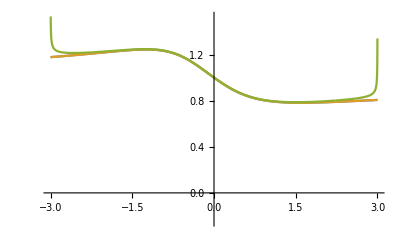

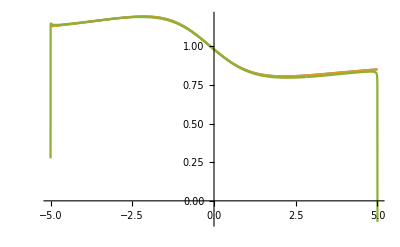

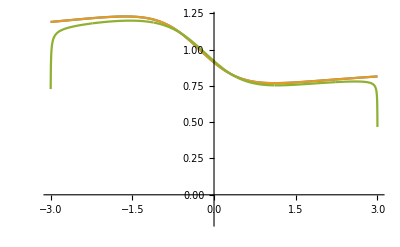

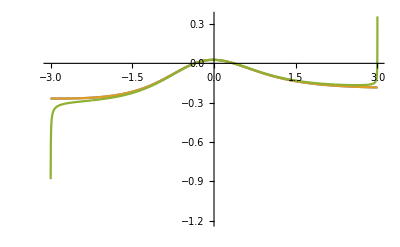

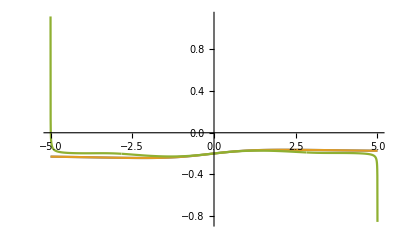

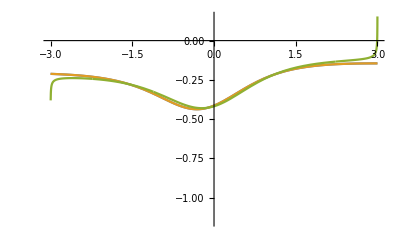

```mathematica
(* Introducing J00 *)
tilJ00[z5_]:=Sqrt[J002[z5]]; (* J00 as square root of  via Monodromy matrix *)
tilJJJ00[z5_]:=Sqrt[JJJ002[z5]]; (* J00 as square root of  via polynomials *)

(* Rprod = 1+R*R *)
Rprod[z5_]:=Sqrt[(2 w[z5])/(F[z5]+w[z5])]; (* sqrt(1+R*R) via polynomials *)
Rprodd[z5_]:=Sqrt[1+R[z5]Conjugate[R[Conjugate[z5]]]]; (* sqrt(1+R*R) directly *)

JJ001[t2_]:=I R[Re[λ[[1]]]+t2 I+10^(-6)] Rprodd[Re[λ[[1]]]+t2 I-10^(-6)]/(-Rprodd[Re[λ[[1]]]+t2 I+10^(-6)]); (* J00 via limits on the first band *)
JJ002[t2_]:=I R[Re[λ[[2]]]+t2 I+10^(-6)] (-Rprodd[Re[λ[[2]]]+t2 I-10^(-6)])/(-Rprodd[Re[λ[[2]]]+t2 I+10^(-6)]); (* J00 via limits on the second band *)
JJ003[t2_]:=I R[Re[λ[[3]]]+t2 I+10^(-6)] (-Rprodd[Re[λ[[3]]]+t2 I-10^(-6)])/Rprodd[Re[λ[[3]]]+t2 I+10^(-6)]; (* J00 via limits on the second band *)
Re[λ[[1]]]
Re[λ[[2]]]
Re[λ[[3]]]

Print["Blue- via monodromy; Orange - via polynomials; Green - via limits"]
Plot[{Re[tilJ00[Re[λ[[3]]]+10^-10+I y]],Re[tilJJJ00[Re[λ[[3]]]+10^-10+I y]],Re[JJ003[y]]},{y,-3,3}, PlotRange->All] (* three pictures should coincide*)
Plot[{Re[tilJ00[Re[λ[[2]]]+10^-10+I y]],Re[tilJJJ00[Re[λ[[2]]]+10^-10+I y]],Re[JJ002[y]]},{y,-5,5}, PlotRange->All]
Plot[{Re[tilJ00[Re[λ[[1]]]+10^-10+I y]],Re[tilJJJ00[Re[λ[[1]]]+10^-10+I y]],Re[JJ001[y]]},{y,-3,3}, PlotRange->All]

Plot[{Im[tilJ00[Re[λ[[3]]]+10^-10+I y]],Im[tilJJJ00[Re[λ[[3]]]+10^-10+I y]],Im[JJ003[y]]},{y,-3,3}, PlotRange->All] (* three pictures should coincide*)
Plot[{Im[tilJ00[Re[λ[[2]]]+10^-10+I y]],Im[tilJJJ00[Re[λ[[2]]]+10^-10+I y]],Im[JJ002[y]]},{y,-5,5}, PlotRange->All]
Plot[{Im[tilJ00[Re[λ[[1]]]+10^-10+I y]],Im[tilJJJ00[Re[λ[[1]]]+10^-10+I y]],Im[JJ001[y]]},{y,-3,3}, PlotRange->All]
```

Initial phases = {0.1,0.2,0.3}

Received phases = {0.100702+7.40674×10^-9 ⅈ,0.200026+6.53631×10^-9 ⅈ,0.299335-1.52129×10^-8 ⅈ}

Integrand 1st band

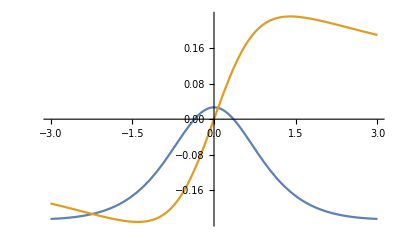

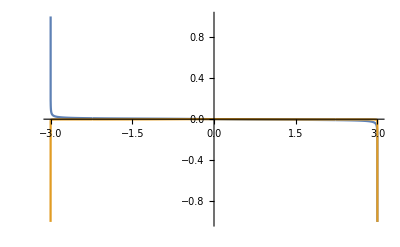

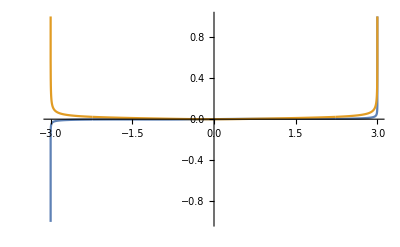

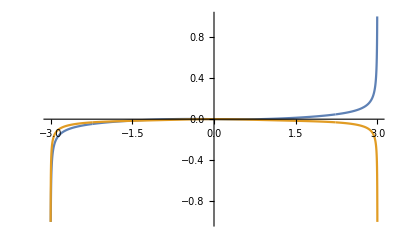

Integrand 2d band

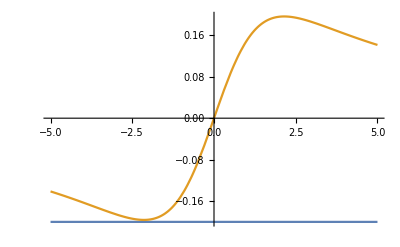

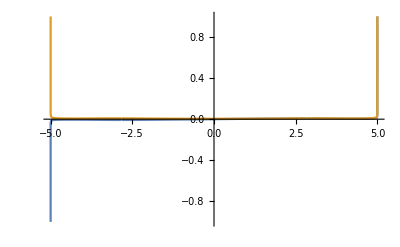

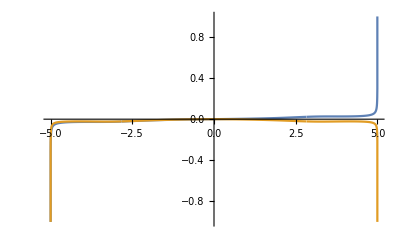

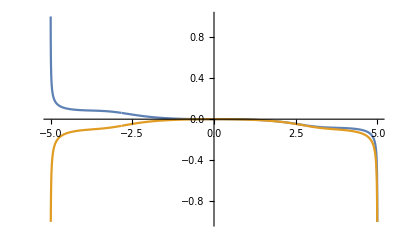

Integrand 3d band

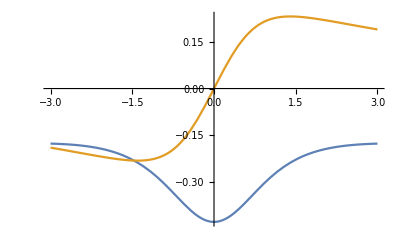

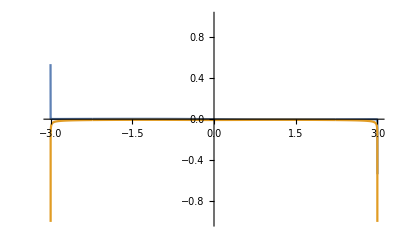

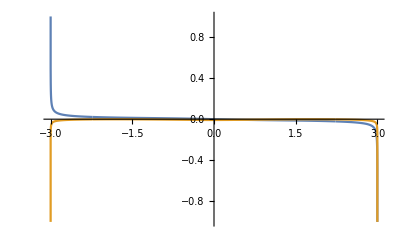

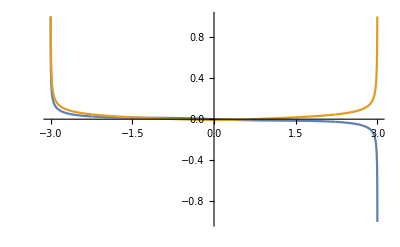

```mathematica
(* ----------------------- Direct problem using J00 defined via monodromy matrix -------------------- *)
Pp[k_]:=Log[tilJ00[k]]+1Log[(k-Conjugate[mu1])/(k-mu1)]+1Log[(k-Conjugate[mu2])/(k-mu2)];
Pm[k_]:=Log[-tilJ00[k]]+1Log[(k-Conjugate[mu1])/(k-mu1)]+1Log[(k-Conjugate[mu2])/(k-mu2)]; 
Off[InterpolatingFunction::dmval]
B=ConstantArray[0, n+1];
For[k=1, k≤n+1, k++,
Pcurp=Interpolation[Table[{x, Pp[Re[λ[[1]]]+I x]},{x, -Im[λ[[1]]], Im[λ[[1]]], (2Im[λ[[1]]])/nλ}]];
Pcurm=Interpolation[Table[{x, Pm[Re[λ[[1]]]+I x]},{x, -Im[λ[[1]]], Im[λ[[1]]], (2Im[λ[[1]]])/nλ}]];

B[[k]]=B[[k]]-N[NIntegrate[(I Pcurp[x](Re[λ[[1]]]+I x)^(k-1))/w[(Re[λ[[1]]]+I x-10^-10)],{x,  -Im[λ[[1]]], Im[λ[[1]]]}]];
];
For[k=1, k≤n+1, k++,
Pcurp=Interpolation[Table[{x, Pp[Re[λ[[2]]]+I x]},{x, -Im[λ[[2]]], Im[λ[[2]]], (2Im[λ[[2]]])/nλ}]];(*vertical*)
Pcurm=Interpolation[Table[{x, Pm[Re[λ[[2]]]+I x]},{x, -Im[λ[[2]]], Im[λ[[2]]], (2Im[λ[[2]]])/nλ}]];
B[[k]]=B[[k]]-N[NIntegrate[(I Pcurp[x](Re[λ[[2]]]+I x)^(k-1))/w[(Re[λ[[2]]]+I x-10^-10)],{x,  -Im[λ[[2]]], Im[λ[[2]]]}]];
];
For[k=1, k≤n+1, k++,
Pcurp=Interpolation[Table[{x, Pp[Re[λ[[3]]]+I x]},{x,-Im[λ[[3]]], Im[λ[[3]]], (2Im[λ[[3]]])/nλ}]];(*vertical*)
Pcurm=Interpolation[Table[{x, Pm[Re[λ[[3]]]+I x]},{x, -Im[λ[[3]]], Im[λ[[3]]], (2Im[λ[[3]]])/nλ}]];
B[[k]]=B[[k]]-N[NIntegrate[(I Pcurp[x](Re[λ[[3]]]+I x)^(k-1))/w[(Re[λ[[3]]]+I x-10^-10)],{x,  -Im[λ[[3]]], Im[λ[[3]]]}]];
];
KK=Table[K[k, j], {k, 1, n+1}, {j, 1, n+1}];
ϕout4=Inverse[I KK].(B);
Print["Initial phases = ",N[ϕ]];
Print["Received phases = ", N[ϕout4]];
Print["Integrand 1st band"];
Pcurp1=Interpolation[Table[{x, Pp[Re[λ[[1]]]+I x]},{x, -Im[λ[[1]]], Im[λ[[1]]], (2Im[λ[[1]]])/nλ}]];
Plot[{Im[Pcurp1[x]],Re[Pcurp1[x]]},{x,  -Im[λ[[1]]], Im[λ[[1]]]}, PlotRange->All]

Plot[{Im[(I Pcurp1[x](Re[λ[[1]]]+I x)^0)/w[(Re[λ[[1]]]+I x-10^-10)]],Re[(I Pcurp1[x](Re[λ[[1]]]+I x)^0)/w[(Re[λ[[1]]]+I x-10^-10)]]},{x,  -Im[λ[[1]]], Im[λ[[1]]]}, PlotRange->{-1,1}]
Plot[{Im[(I Pcurp1[x](Re[λ[[1]]]+I x)^1)/w[(Re[λ[[1]]]+I x-10^-10)]],Re[(I Pcurp1[x](Re[λ[[1]]]+I x)^1)/w[(Re[λ[[1]]]+I x-10^-10)]]},{x,  -Im[λ[[1]]], Im[λ[[1]]]},  PlotRange->{-1,1}]
Plot[{Im[(I Pcurp1[x](Re[λ[[1]]]+I x)^2)/w[(Re[λ[[1]]]+I x-10^-10)]],Re[(I Pcurp1[x](Re[λ[[1]]]+I x)^2)/w[(Re[λ[[1]]]+I x-10^-10)]]},{x,  -Im[λ[[1]]], Im[λ[[1]]]}, PlotRange->{-1,1}]

Print["Integrand 2d band"];
Pcurp2=Interpolation[Table[{x, Pp[Re[λ[[2]]]+I x]},{x, -Im[λ[[2]]], Im[λ[[2]]], (2Im[λ[[2]]])/nλ}]];
Plot[{Im[Pcurp2[x]],Re[Pcurp2[x]]},{x,  -Im[λ[[2]]], Im[λ[[2]]]}, PlotRange->All]

Plot[{Im[(I Pcurp2[x](Re[λ[[2]]]+I x)^0)/w[(Re[λ[[2]]]+I x-10^-10)]],Re[(I Pcurp2[x](Re[λ[[2]]]+I x)^0)/w[(Re[λ[[2]]]+I x-10^-10)]]},{x,  -Im[λ[[2]]], Im[λ[[2]]]}, PlotRange->{-1,1}]
Plot[{Im[(I Pcurp2[x](Re[λ[[2]]]+I x)^1)/w[(Re[λ[[2]]]+I x-10^-10)]],Re[(I Pcurp2[x](Re[λ[[2]]]+I x)^1)/w[(Re[λ[[2]]]+I x-10^-10)]]},{x,  -Im[λ[[2]]], Im[λ[[2]]]},  PlotRange->{-1,1}]
Plot[{Im[(I Pcurp2[x](Re[λ[[2]]]+I x)^2)/w[(Re[λ[[2]]]+I x-10^-10)]],Re[(I Pcurp2[x](Re[λ[[2]]]+I x)^2)/w[(Re[λ[[2]]]+I x-10^-10)]]},{x,  -Im[λ[[2]]], Im[λ[[2]]]}, PlotRange->{-1,1}]

Print["Integrand 3d band"];
Pcurp3=Interpolation[Table[{x, Pp[Re[λ[[3]]]+I x]},{x,-Im[λ[[3]]], Im[λ[[3]]], (2Im[λ[[3]]])/nλ}]];
Plot[{Im[Pcurp3[x]],Re[Pcurp3[x]]},{x,  -Im[λ[[1]]], Im[λ[[1]]]}, PlotRange->All]

Plot[{Im[(I Pcurp3[x](Re[λ[[3]]]+I x)^0)/w[(Re[λ[[3]]]+I x-10^-10)]],Re[(I Pcurp3[x](Re[λ[[3]]]+I x)^0)/w[(Re[λ[[3]]]+I x-10^-10)]]},{x,  -Im[λ[[3]]], Im[λ[[3]]]}, PlotRange->{-1,1}]
Plot[{Im[(I Pcurp3[x](Re[λ[[3]]]+I x)^1)/w[(Re[λ[[3]]]+I x-10^-10)]],Re[(I Pcurp3[x](Re[λ[[3]]]+I x)^1)/w[(Re[λ[[3]]]+I x-10^-10)]]},{x,  -Im[λ[[3]]], Im[λ[[3]]]},  PlotRange->{-1,1}]
Plot[{Im[(I Pcurp3[x](Re[λ[[3]]]+I x)^2)/w[(Re[λ[[3]]]+I x-10^-10)]],Re[(I Pcurp3[x](Re[λ[[3]]]+I x)^2)/w[(Re[λ[[3]]]+I x-10^-10)]]},{x,  -Im[λ[[3]]], Im[λ[[3]]]}, PlotRange->{-1,1}]
```